## Manual for GRSpectral.m (To be completed)

The Mathematica package GRSpectral.m (by Jie Ren, available at https://github.com/renphysics/GRSpectral ) is designed for solving PDEs by the pseudospectral method.

### Install and load the package

Put the file GRSpectral.m in the following directory (or the same directory as the working notebook)

```mathematica
SystemOpen@FileNameJoin[{$UserBaseDirectory,"Applications"}]  (*Put "*.m" in*)
```

Load the package by running

```mathematica
<<GRSpectral.m
```

## Example 1: Holographic superconductors in 0803.3295 (HHH)

We start from the two coupled equations. They are copied from Herzog’s notebook by the shooting method.

```mathematica
restart[];
flist={psi[z],phi[z]};
eqlist={(-z+z^4+phi[z]^2) psi[z]+(-1+z^3) (3 z^2 psi'[z]+(-1+z^3) psi''[z]),2 phi[z] psi[z]^2+(-1+z^3) phi''[z]}; (*Equations of motion*)
bdylist1={psi'[z],phi[z]-mu}; (*Boundary conditions at z=0*)
bdylist2={3 z^2 psi'[z]-2psi[z],phi[z]}; (*Boundary conditions at z=1*)
eqProcess[flist,eqlist,{{z==0,bdylist1},{z==1,bdylist2}}]; (*Impose boundary conditions*)
calcfref:=(psi=one; phi=mu one;);  (*Initial guess of the solution*)
output:=(solsave);
```

```mathematica
spNDSolve[z,linearMap[{0,1}],60,{mu,2}];
```

```mathematica
phi
```

{2.,1.99863,1.99452,1.98769,1.97815,1.96593,1.95106,1.93358,1.91355,1.89101,1.86603,1.83867,1.80902,1.77715,1.74314,1.70711,1.66913,1.62932,1.58779,1.54464,1.5,1.45399,1.40674,1.35837,1.30902,1.25882,1.20791,1.15643,1.10453,1.05234,1.,0.947664,0.895472,0.843566,0.792088,0.741181,0.690983,0.641632,0.593263,0.54601,0.5,0.455361,0.412215,0.37068,0.330869,0.292893,0.256855,0.222854,0.190983,0.161329,0.133975,0.108993,0.0864545,0.0664196,0.0489435,0.0340742,0.0218524,0.0123117,0.0054781,0.00137047,0.}

### Example 1’: Holographic superconductors in 0803.3295 (HHH)

This example is the same as the last one, but with difference in details. (1) the equations of motion contain a function f[z]. (2) There are singularities at z=1. (3) The equations are saved to a file.

```mathematica
restart[];
flist={psi[z],phi[z]};
reflist={f[z]}; (*other functions in equations*)
eqlist={(z ((-z+z^4+phi[z]^2) psi[z]+(-1+z^3) (3 z^2 psi'[z]+(-1+z^3) psi''[z])))/((-1+z^3)^2),(2 phi[z] psi[z]^2+(-1+z^3) phi''[z])/(-1+z^3)};
eqProcess[{flist,reflist},put[eqlist]];
```

Once the equations of motion are saved to a file “eqlistmat”, the follwing is the code to run.

```mathematica
restart[];
flist={psi[z],phi[z]}; (*unkown functions to be solved*)
reflist={f[z]}; (*other functions in equations*)
bdylist1={psi'[z],phi[z]-mu}; (*Boundary conditions at z=0*)
bdylist2={3 z^2 psi'[z]-2psi[z],phi[z]}; (*Boundary conditions at z=1*)
eqProcess[{flist,reflist},get[eqlistmat,z->zaux12],{{z==0,bdylist1},{z==1,bdylist2}}];  (*load equations from a file; replace z with zaux12 to avoid singularities at two boundaries*)(*Jacobian of boundary conditions*)
calcfref:=(psi=one; phi=mu one; f=1-z^3);  (*Initial guess of the solution*)
calcref:=(f=1-z^3);
output:=(solsave);
```

```mathematica
Dynamic[changes]
```

```mathematica
spNDSolve[z,linearMap[{0,1}],nz,{nz,60},{mu,2},eqlistmatQ->True];
```

```mathematica
phi
```

{2.,1.99863,1.99452,1.98769,1.97815,1.96593,1.95106,1.93358,1.91355,1.89101,1.86603,1.83867,1.80902,1.77715,1.74314,1.70711,1.66913,1.62932,1.58779,1.54464,1.5,1.45399,1.40674,1.35837,1.30902,1.25882,1.20791,1.15643,1.10453,1.05234,1.,0.947664,0.895472,0.843566,0.792088,0.741181,0.690983,0.641632,0.593263,0.54601,0.5,0.455361,0.412215,0.37068,0.330869,0.292893,0.256855,0.222854,0.190983,0.161329,0.133975,0.108993,0.0864545,0.0664196,0.0489435,0.0340742,0.0218524,0.0123117,0.0054781,0.00137047,0.}

## Example 2: Einstein-scalar system in 2206.03498

### Obtain the EOMs

```mathematica
coord={t,z,x,y};
metric=1/z^2({{-g[z]/h[z], 0, 0, 0}, {0, 1/g[z], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});
metricsign=-1;
<<diffgeo.m
myphi=phi[z];
scalarTT=covariant[myphi]**covariant[myphi]+2/(dimen-2)metric myV[myphi]//Simplify;
einsteinEq=RicciTensor-1/2(scalarTT)//Simplify
scalarEq=scalarLaplacian[myphi]-myV'[myphi]//Simplify
```

{{1/(4 z^2 h[z]^3)g[z] (h[z] (-3 z^2 g'[z] h'[z]+2 h[z] (myV[phi[z]]-4 z g'[z]+z^2 g''[z]))+g[z] (12 h[z]^2+3 z^2 h'[z]^2-2 z h[z] (-3 h'[z]+z h''[z]))),0,0,0},{0,1/(4 z^2 g[z] h[z]^2)(h[z] (3 z^2 g'[z] h'[z]-2 h[z] (myV[phi[z]]-4 z g'[z]+z^2 g''[z]))-g[z] (3 z^2 h'[z]^2+2 h[z]^2 (6+z^2 phi'[z]^2)+2 z h[z] (h'[z]-z h''[z]))),0,0},{0,0,-(h[z] (myV[phi[z]]-2 z g'[z])+g[z] (6 h[z]+z h'[z]))/(2 z^2 h[z]),0},{0,0,0,-(h[z] (myV[phi[z]]-2 z g'[z])+g[z] (6 h[z]+z h'[z]))/(2 z^2 h[z])}}

-myV'[phi[z]]+z^2 g'[z] phi'[z]+1/2 z g[z] ((-4-(z h'[z])/h[z]) phi'[z]+2 z phi''[z])

### Solve EOMs with boundary conditions

```mathematica
restart[]; (*No need to quit kernel*)
myV[ϕ_]:=(2 ⅇ^(-ϕ/α) (α^2-8 ⅇ^(((1+α^2) ϕ)/(2 α)) α^2-3 α^4+ⅇ^(ϕ/α+α ϕ) (-3+α^2)))/((1+α^2)^2);
eqlist={2 myV[phi[z]]-4 z g'[z]+g[z] (12+z^2 phi'[z]^2),2 h'[z]-z h[z] phi'[z]^2,-z^2 g[z] h'[z] phi'[z]+h[z] (-2 myV'[phi[z]]+z (-4 g[z] phi'[z]+2 z g'[z] phi'[z]+2 z g[z] phi''[z]))};
bdylist1={g[z],h[z]-1,phi''[z]-2κ phi'[z]};
bdylist2={g[z],h[z]-1,-2 myV'[phi[z]]+2 g'[z] phi'[z]};
eqProcess[{g[z],h[z],phi[z]},eqlist,{{{z==0,{2,3}},bdylist1},{{z==1,{1,3}},bdylist2}}];
calcfref:=(g=1/5(1-z); h=one; phi=(1/2z+1/4 z^2););
output:={(-(dz.g)/(4Pi √h(-κ)))[[-1]],((dz.phi)/-κ)[[1]],(4Pi)/κ^2,1/(-κ)^3(-1/3 dz.dzz.(g/h))[[1]],1/(-κ)^3(1/6 dz.dzz.g-1/4(dz.phi)(dzz.phi))[[1]],3/(4Pi(-κ)),-1/(-κ)^3,κ,1/(-κ)^3(-1/3 dz.dzz.g+3/4(dz.phi)(dzz.phi))[[1]],solsave}; 
(*T/(-κ), O/(-κ), s/κ^2, ϵ0/(-κ)^3, F/(-κ)^3; Ts=3/2 ϵ0*)
Dynamic[changes]
```

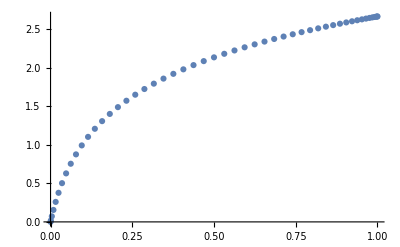

```mathematica
spNDSolve[z,linearMap[{0,1}],50,{α,0.3,0.4,0.1},{ρ,0.},{κ,-2,-10,-1/2},minPrec->MachinePrecision]; (*minPrec: specify the precision: MachinePrecision or an integer*)
ListPlot[{z,phi}ᵀ]
```

```mathematica
spNDSolve[z,linearMap[{0,1}],50,{α,4/10},{ρ,0},{κ,-1/2,-35/100,1/100},epValue->10^-8,minPrec->34]; (*phi>0, increase T*)
```

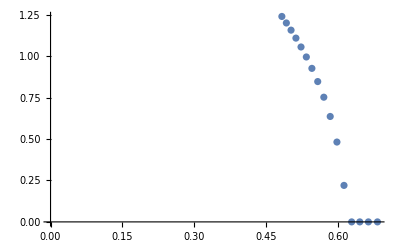

```mathematica
ListPlot[outputs[[;;,{1,2}]],PlotRange->All,AxesOrigin->{0,0}]
```

```mathematica
outT:=outputs[[;;,1]];
outO:=outputs[[;;,2]];
outS:=outputs[[;;,3]];
outF:=outputs[[;;,5]];
outT0:=outputs[[;;,6]];
outF0:=outputs[[;;,7]];
outκ:=outputs[[;;,8]];
outM:=outputs[[;;,9]];
outphih:=outputs[[;;,-1,3,-1]];
```

### spNDSolve

```mathematica
Options[spNDSolve]
```

{calcrefredQ→False,epValue→1/1000000000,eqlistmatQ→False,iniQ→True,linearQ→False,lsqrQ→False,maxChange→1000000000,minPrec→0,D→False}

epValue: When the change for an iteration is smaller than the epValue, the iteration will stop.

eqlistmatQ: If the equations and there Jacobian are saved to a file, this option must be set to be True.

iniQ: If this is True, then the initial guess of the solution is given by calcfref. If it is False, then not run calcfref.

linearQ: If the equations are linear, this must be set to be True.

lsqrQ: If this is True, then use LeastSquare instead of LinearSolve.

minPrec: If it is zero, then use machine precision. If it is nonzero, then use specified precision.

“D”->n: Delete the rows and columns corresponding to boundaries with label n.

### cheb: Construct the grid

The function for constructing the grid is cheb. It has flexible capabilities by different formats.

```mathematica
cheb[x,8]
```

```mathematica
dx//MatrixForm
```

(-21.5 | 26.2741 | -6.82843 | 3.23983 | -2. | 1.44646 | -1.17157 | 1.03957 | -0.5
-6.56854 | 3.15432 | 4.61313 | -1.84776 | 1.08239 | -0.765367 | 0.613126 | -0.541196 | 0.259892
1.70711 | -4.61313 | 0.707107 | 3.08239 | -1.41421 | 0.917608 | -0.707107 | 0.613126 | -0.292893
-0.809957 | 1.84776 | -3.08239 | 0.224171 | 2.61313 | -1.30656 | 0.917608 | -0.765367 | 0.361616
0.5 | -1.08239 | 1.41421 | -2.61313 | 0. | 2.61313 | -1.41421 | 1.08239 | -0.5
-0.361616 | 0.765367 | -0.917608 | 1.30656 | -2.61313 | -0.224171 | 3.08239 | -1.84776 | 0.809957
0.292893 | -0.613126 | 0.707107 | -0.917608 | 1.41421 | -3.08239 | -0.707107 | 4.61313 | -1.70711
-0.259892 | 0.541196 | -0.613126 | 0.765367 | -1.08239 | 1.84776 | -4.61313 | -3.15432 | 6.56854
0.5 | -1.03957 | 1.17157 | -1.44646 | 2. | -3.23983 | 6.82843 | -26.2741 | 21.5)

```mathematica
dx.x
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
dxx.x^2
```

{2.,2.,2.,2.,2.,2.,2.,2.,2.}

In the above example, cheb[x, 8] can be cheb[u, 8], then the variable will be u, and differential matrix is du and duu.     id is the idensity matrix, zero is the zero matrix, and one is a vector of 1’s.

```mathematica
cheb[x,#&,8]
```

```mathematica
cheb[x,(#+1)/2&,8]
```

```mathematica
cheb[x,linearMap[{0,1}],8]
```

linearMap[{x1, x2} -> {y1, y2}] generates a pure function that linearly maps the interval (x1, x2) to (y1, y2). linearMap[{x1, x2}] generates a pure function that linearly maps the interval (x1, x2) to (-1, 1).

```mathematica
cheb[x,{10,"periodic"}]
```

```mathematica
x
```

{0.,0.571199,1.1424,1.7136,2.28479,2.85599,3.42719,3.99839,4.56959,5.14079,5.71199}

```mathematica
dx.Sin[x]
```

{1.,0.841254,0.415415,-0.142315,-0.654861,-0.959493,-0.959493,-0.654861,-0.142315,0.415415,0.841254}

```mathematica
Cos[x]
```

{1.,0.841254,0.415415,-0.142315,-0.654861,-0.959493,-0.959493,-0.654861,-0.142315,0.415415,0.841254}

```mathematica
cheb[x,{10,4}]
```

```mathematica
x
```

{-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.}

```mathematica
dx//MatrixForm
```

(-10.4167 | 20. | -15. | 6.66667 | -1.25 | 0 | 0 | 0 | 0 | 0 | 0
-1.25 | -4.16667 | 7.5 | -2.5 | 0.416667 | 0 | 0 | 0 | 0 | 0 | 0
0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.416667 | -3.33333 | 0 | 3.33333 | -0.416667
0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 2.5 | -7.5 | 4.16667 | 1.25
0 | 0 | 0 | 0 | 0 | 0 | 1.25 | -6.66667 | 15. | -20. | 10.4167)

cheb[x, {10, 4, "cheb"}] or cheb[x, {10, 4, “periodic”}]

```mathematica
cheb[x1,linearMap[{0,0.2}],6,"1"]
cheb[x2,linearMap[{0.2,1}],8,"2"]
```

```mathematica
cheb[{x,y},{10,10}]
```

```mathematica
cheb[{x,y},{#&,#&},{10,10}]
```

```mathematica
cheb[{z,x},{linearMap[{0,1}],#&},{20,{20,"periodic"}}]
```

```mathematica
cheb[{z1,x1},{linearMap[{0,0.2}],#&},{20,{20,"periodic"}},"1"]
cheb[{z2,x2},{linearMap[{0.2,1}],#&},{20,{20,"periodic"}},"2"]
```

```mathematica
cheb[x,8]
```

```mathematica
x                                                      (*Collocation points*)
```

{-1.,-0.92388,-0.707107,-0.382683,0.,0.382683,0.707107,0.92388,1.}

```mathematica
f=1-x^3                                      (*A function is a vector*)
```

{2.,1.78858,1.35355,1.05604,1.,0.943957,0.646447,0.211419,0.}

```mathematica
dx//MatrixForm                      (*Differentiation matrix*)
```

(-21.5 | 26.2741 | -6.82843 | 3.23983 | -2. | 1.44646 | -1.17157 | 1.03957 | -0.5
-6.56854 | 3.15432 | 4.61313 | -1.84776 | 1.08239 | -0.765367 | 0.613126 | -0.541196 | 0.259892
1.70711 | -4.61313 | 0.707107 | 3.08239 | -1.41421 | 0.917608 | -0.707107 | 0.613126 | -0.292893
-0.809957 | 1.84776 | -3.08239 | 0.224171 | 2.61313 | -1.30656 | 0.917608 | -0.765367 | 0.361616
0.5 | -1.08239 | 1.41421 | -2.61313 | 0. | 2.61313 | -1.41421 | 1.08239 | -0.5
-0.361616 | 0.765367 | -0.917608 | 1.30656 | -2.61313 | -0.224171 | 3.08239 | -1.84776 | 0.809957
0.292893 | -0.613126 | 0.707107 | -0.917608 | 1.41421 | -3.08239 | -0.707107 | 4.61313 | -1.70711
-0.259892 | 0.541196 | -0.613126 | 0.765367 | -1.08239 | 1.84776 | -4.61313 | -3.15432 | 6.56854
0.5 | -1.03957 | 1.17157 | -1.44646 | 2. | -3.23983 | 6.82843 | -26.2741 | 21.5)

```mathematica
dx.f
```

```mathematica
cheb[x,(#+1)/2&,20]
```

```mathematica
cheb[x,linearMap[{0,1}],8]
```

```mathematica
cheb[x,{20,"periodic"}]
```

```mathematica
cheb[x,linearMap[{0,1}],{50,4}]
```

```mathematica
cheb[{z,x},{linearMap[{0,1}],#&},{20,{20,"periodic"}}]
```

```mathematica
cheb[{z1,x1},{linearMap[{0,0.2}],#&},{20,{20,"periodic"}},"1"]
cheb[{z2,x2},{linearMap[{0.2,1}],#&},{20,{20,"periodic"}},"2"]
```